```mathematica
$PrePrint=#/. {Csc[z_]:>1/Defer@Sin[z],Sec[z_]:>1/Defer@Cos[z]}&;

Clear[a1,b1,a2,b2,i];rep={a1->Subscript[a, 1],a2->Subscript[a, 2],b1->Subscript[b, 1],b2->Subscript[b, 2],κi->Subscript[κ, i],κr->Subscript[κ, r], ky->Subscript[k, y], kz->Subscript[k, z],en->e};
ass=Assumptions->{ξ,vz,v,k,kp,θ,ϕ,θp,ϕp,kx,ky,kz,ek,ang}∈ Reals &&  k>0 && kp>0 && ek>0 && v>0 && vz>0;
(*** Gell Mann Matrices; https://en.wikipedia.org/wiki/Structure_constants **)
λ1=({{0, 1, 0}, {1, 0, 0}, {0, 0, 0}});λ2=({{0, -ⅈ, 0}, {ⅈ, 0, 0}, {0, 0, 0}});λ3=({{1, 0, 0}, {0, -1, 0}, {0, 0, 0}});λ4=({{0, 0, 1}, {0, 0, 0}, {1, 0, 0}});λ5=({{0, 0, -ⅈ}, {0, 0, 0}, {ⅈ, 0, 0}});
λ6=({{0, 0, 0}, {0, 0, 1}, {0, 1, 0}});λ7=({{0, 0, 0}, {0, 0, -ⅈ}, {0, ⅈ, 0}});λ8=1/(√3)({{1, 0, 0}, {0, 1, 0}, {0, 0, -2}});id=({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}});
λ={λ1,λ2,λ3,λ4,λ5,λ6,λ7,λ8};
```

```mathematica
(****** 3-band Berrry-dipole node: -Graphics- *******)
h3=kx λ1+ky λ2+kz λ5;
FullSimplify[Eigensystem[h3],ass]
hψ=kx λ1ψ+ky λ2ψ+kz λ5ψ/.{kx->-ⅈ Dx}
```

{{0,-√(kx^2+ky^2+kz^2),√(kx^2+ky^2+kz^2)},{{0,(ⅈ kz)/(kx-ⅈ ky),1},{(ⅈ √(kx^2+ky^2+kz^2))/kz,(-ⅈ kx+ky)/kz,1},{-(ⅈ √(kx^2+ky^2+kz^2))/kz,(-ⅈ kx+ky)/kz,1}}}

-ⅈ Dx λ1ψ+ky λ2ψ+kz λ5ψ

```mathematica
Clear[ψ,eq0,eq,eqn,sol,solu,κ,κr,κi,b1,b2,α];
κ=κr+ⅈ κi;
ψ={1,a1+ⅈ b1,a2+ⅈ b2};
ψdag={1,a1-ⅈ b1,a2-ⅈ b2};
prod=FullSimplify[ψdag.(λ1.ψ),ass]/2;
eq0=Flatten[FullSimplify[ComplexExpand[ReIm[prod]],ass],1]
ψ/.a1->0
```

{a1,0}

{1,ⅈ b1,a2+ⅈ b2}

```mathematica
({-en+b2 kz-a1 κi+b1 (ky-κr),-a2 kz-b1 κi+a1 (-ky+κr),-a1 en-κi,-b1 en+ky+κr,-a2 en,-b2 en+kz}/.a1->0)/.rep
{e (Subscript[a, 2]+ⅈ Subscript[b, 2]),ⅈ Subscript[k, z]}//TeXForm;
```

{-e+b_2 k_z+b_1 (k_y-κ_r),-a_2 k_z-b_1 κ_i,-κ_i,-e b_1+k_y+κ_r,-e a_2,-e b_2+k_z}

```mathematica
Clear[ψ];ψ={1,a1+ⅈ b1,a2+ⅈ b2};
eq=FullSimplify[ⅈ (κr+ⅈ κi) λ1.ψ+ky λ2.ψ+kz λ5.ψ -en id.ψ,ass]
eqn=Flatten[FullSimplify[ComplexExpand[ReIm[eq]],ass],1]
solu=FullSimplify[Solve[ a1 ==0 && eqn[[1]]==0 && eqn[[2]]==0 && eqn[[3]]==0 && eqn[[4]]==0 && eqn[[5]]==0 && eqn[[6]]==0  && κr≠0,{en,κr,κi,a1,b1,a2,b2}],ass]
sol[ky_,kz_]={en,κr}/.solu;
Clear[κ,κi,b1,b2,en];
```

{-en+(-ⅈ a2+b2) kz+(-ⅈ a1+b1) (ky-ⅈ κi-κr),-((a1+ⅈ b1) en)+ⅈ (ky+ⅈ κi+κr),-((a2+ⅈ b2) en)+ⅈ kz}

{-en+b2 kz-a1 κi+b1 (ky-κr),-a2 kz-b1 κi+a1 (-ky+κr),-a1 en-κi,-b1 en+ky+κr,-a2 en,-b2 en+kz}

Solve::svars: Equations may not give solutions for all "solve" variables.

{{en→(b1 ky-√(kz^2+b1^2 (ky^2+kz^2)))/(1+b1^2),κr→-(ky+b1 √(kz^2+b1^2 (ky^2+kz^2)))/(1+b1^2),κi→0,a1→0,a2→0,b2→-(b1 ky+√(kz^2+b1^2 (ky^2+kz^2)))/kz},{en→(b1 ky+√(kz^2+b1^2 (ky^2+kz^2)))/(1+b1^2),κr→(-ky+b1 √(kz^2+b1^2 (ky^2+kz^2)))/(1+b1^2),κi→0,a1→0,a2→0,b2→(-b1 ky+√(kz^2+b1^2 (ky^2+kz^2)))/kz},{en→-(ⅈ kz^2)/(2 ky),κr→-ky-kz^2/(2 ky),κi→0,a1→0,b1→-ⅈ,a2→0,b2→(2 ⅈ ky)/kz},{en→(ⅈ kz^2)/(2 ky),κr→-ky-kz^2/(2 ky),κi→0,a1→0,b1→ⅈ,a2→0,b2→-(2 ⅈ ky)/kz}}

```mathematica
(* where κr vanishes, what is the energy value? 
{en->(b1 ky-√(kz^2+b1^2 (ky^2+kz^2)))/(1+b1^2),κr->-(ky+b1 √(kz^2+b1^2 (ky^2+kz^2)))/(1+b1^2),κi->0,a2->0,b2->-(b1 ky+√(kz^2+b1^2 (ky^2+kz^2)))/kz}*)
Clear[b1val];b1val=Flatten[FullSimplify[Solve[0==ky+b1 √(kz^2+b1^2 (ky^2+kz^2)) ,b1],ass],1]
FullSimplify[(b1 ky-√(kz^2+b1^2 (ky^2+kz^2)))/(1+b1^2)/.-ky/(√(ky^2+kz^2)),ass]
Clear[kx,ky,kz];(* correct soln for μ<0 *)
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{b1→-ⅈ,b1→ⅈ,b1→-ky/(√(ky^2+kz^2))}

-√(ky^2+kz^2)

```mathematica
(* where κr vanishes, what is the energy value? 
{en->(b1 ky+√(kz^2+b1^2 (ky^2+kz^2)))/(1+b1^2),κr->(-ky+b1 √(kz^2+b1^2 (ky^2+kz^2)))/(1+b1^2),κi->0,a2->0,b2->(-b1 ky+√(kz^2+b1^2 (ky^2+kz^2)))/kz}*)
Clear[b1val];b1val=Flatten[FullSimplify[Solve[0==-ky+b1 √(kz^2+b1^2 (ky^2+kz^2)) ,b1],ass],1]

FullSimplify[(b1 ky+√(kz^2+b1^2 (ky^2+kz^2)))/(1+b1^2)/. ky/(√(ky^2+kz^2)),ass]
Clear[kx,ky,kz];(* correct soln for μ>0 *)
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{b1→-ⅈ,b1→ⅈ,b1→ky/(√(ky^2+kz^2))}

√(ky^2+kz^2)

```mathematica
FullSimplify[b1^2(ky^2+kz^2)-ky^2]
(* we must have (1-b1^2) ky^2= b1^2 kz^2 at the edge of the arc=> 1-b1^2>=0*)
```

(-1+b1^2) ky^2+b1^2 kz^2

```mathematica
(* where does κr go to zero and mixes with the bulk states? 
{en->(b1 ky+√(kz^2+b1^2 (ky^2+kz^2)))/(1+b1^2),κr->(-ky+b1 √(kz^2+b1^2 (ky^2+kz^2)))/(1+b1^2),κi->0,a2->0,b2->(-b1 ky+√(kz^2+b1^2 (ky^2+kz^2)))/kz} *)
Clear[bulkentry];

enfa=(b1 ky+√(kz^2+b1^2 (ky^2+kz^2)))/(1+b1^2);bulkentry=DeleteDuplicates[FullSimplify[Solve[enfa==μ && √(kz^2+ky^2)==μ,{ky,kz}],ass]]/.√(-((-1+b1^2) μ^2))->√(-(-1+b1^2))μ
FullSimplify[(* κr = *)(-ky+b1 √(kz^2+b1^2 (ky^2+kz^2)))/(1+b1^2)/.bulkentry,ass]/.√(μ^2)->μ
Print["tangent values"];
grad=FullSimplify[FullSimplify[Grad[enfa,{ky,kz}]/.bulkentry,ass]/.{√(μ^2)->μ,(√(1-b1^2) μ)/(√(μ^2))->√(1-b1^2)}]
tang1={grad[[1,2]],-grad[[1,1]]}
tang2={grad[[2,2]],-grad[[2,1]]}
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{ky→b1 μ,kz→-√(1-b1^2) μ},{ky→b1 μ,kz→√(1-b1^2) μ}}

{0,0}

tangent values

{{b1,-√(1-b1^2)},{b1,√(1-b1^2)}}

{-√(1-b1^2),-b1}

{√(1-b1^2),-b1}

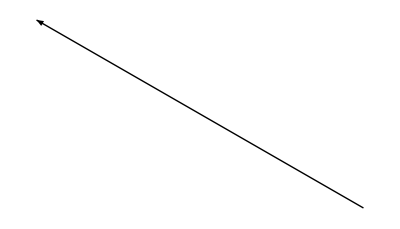

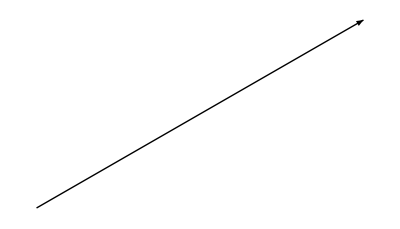

```mathematica
b1=-0.5;Graphics@Arrow[{{0,0},{-√(1-b1^2),-b1}}]
Graphics@Arrow[{{0,0},{√(1-b1^2),-b1}}]
Clear[b1];
```

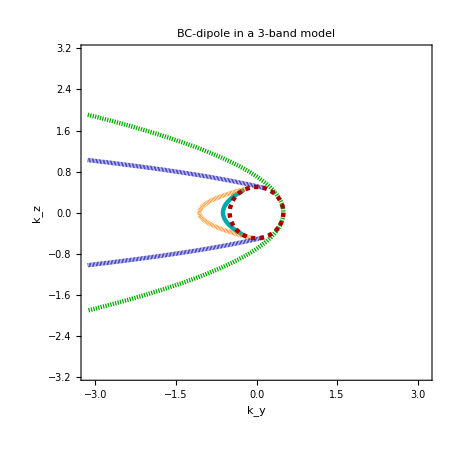

```mathematica
lim=π;mu=0.5;kw=1;th=0.007;
style={Directive[Darker[Cyan],Thickness[th]],(**)Directive[Orange,Thickness[th],Dashing[0.001]],(**)Directive[Darker[Blue],Thickness[th],Dashing[0.001]],(**)Directive[Darker[Green],Thickness[th],Dashing[0.002]]};

b1v={-0.5,-0.25,0.25,1};
i=1;
b1=b1v[[i]];
c1=ContourPlot[(b1 ky+√(kz^2+b1^2 (ky^2+kz^2)))/(1+b1^2)==mu,{ky,-lim,lim},{kz,-lim,lim},ContourStyle->style[[i]],RegionFunction->Function[{ky,kz,z},Chop[-ky+b1 √(kz^2+b1^2 (mu^2))]>=0 ],PlotLegends->Automatic]//Quiet;
i=2;
b1=b1v[[i]];
c2=ContourPlot[(b1 ky+√(kz^2+b1^2 (ky^2+kz^2)))/(1+b1^2)==mu,{ky,-lim,lim},{kz,-lim,lim},ContourStyle->style[[i]],RegionFunction->Function[{ky,kz,z},Chop[-ky+b1 √(kz^2+b1^2 (mu^2))]>=0 ],PlotLegends->Automatic]//Quiet;
i=3;
b1=b1v[[i]];
c3=ContourPlot[(b1 ky+√(kz^2+b1^2 (ky^2+kz^2)))/(1+b1^2)==mu,{ky,-lim,lim},{kz,-lim,lim},ContourStyle->style[[i]],RegionFunction->Function[{ky,kz,z},Chop[-ky+b1 √(kz^2+b1^2 (mu^2))]>=0 ],PlotLegends->Automatic]//Quiet;
i=4;
b1=b1v[[i]];
c4=ContourPlot[(b1 ky+√(kz^2+b1^2 (ky^2+kz^2)))/(1+b1^2)==mu,{ky,-lim,lim},{kz,-lim,lim},ContourStyle->style[[i]],RegionFunction->Function[{ky,kz,z},Chop[-ky+b1 √(kz^2+b1^2 (mu^2))]>=0 ],PlotLegends->Automatic]//Quiet;
fs=ContourPlot[ky^2+kz^2==mu^2,{ky,-lim,lim},{kz,-lim,lim},ContourStyle->Directive[Darker[Red],Dashing[0.007],Thickness[th]]];
pl=Show[c1,c2,c3,c4,fs,Frame->True,Axes->False,FrameTicksStyle->Directive[Bold,Gray,16],LabelStyle->{Black,Bold,22,FontFamily->"TexMaths Symbols"},FrameLabel->{"k_y","k_z"},ImageSize->450,PlotLabel->Style[(****)"BC-dipole in a 3-band model",20,FontFamily->"TexMaths Roman",Brown,Bold]];
leg=LineLegend[style,{b1v[[1]], b1v[[2]], b1v[[3]], b1v[[4]]},LabelStyle->{18,Darker[Brown],Bold},LegendLayout->{"Row",1}];
plt=Legended[GraphicsGrid[{{pl}},ImageSize->450],Placed[leg,Below]]
Clear[kx,mu,kw,b1v,i,b1];
SetDirectory[NotebookDirectory[]];
```

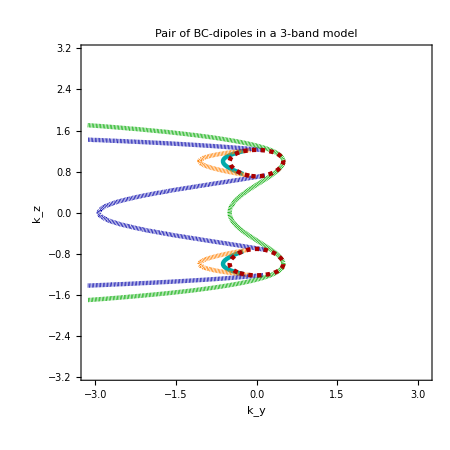

```mathematica
lim=π;mu=0.5;kw=1;th=0.007;
style={Directive[Darker[Cyan],Thickness[th]],(**)Directive[Orange,Thickness[th],Dashing[0.001]],(**)Directive[Darker[Blue],Thickness[th],Dashing[0.001]],(**)Directive[Darker[Green],Thickness[th],Dashing[0.001]]};

b1v={-0.5,-0.25,0.25,1};
i=1;
b1=b1v[[i]];
c1=ContourPlot[(b1 ky+√((kz^2-kw^2)^2+b1^2 (ky^2+(kz^2-kw^2)^2)))/(1+b1^2)==mu,{ky,-lim,lim},{kz,-lim,lim},ContourStyle->style[[i]],RegionFunction->Function[{ky,kz,z},Chop[-ky+b1 √((kz^2-kw^2)^2+b1^2 (mu^2))]>=0 ],PlotLegends->Automatic]//Quiet;
i=2;
b1=b1v[[i]];
c2=ContourPlot[(b1 ky+√((kz^2-kw^2)^2+b1^2 (ky^2+(kz^2-kw^2)^2)))/(1+b1^2)==mu,{ky,-lim,lim},{kz,-lim,lim},ContourStyle->style[[i]],RegionFunction->Function[{ky,kz,z},Chop[-ky+b1 √((kz^2-kw^2)^2+b1^2 (mu^2))]>=0 ],PlotLegends->Automatic]//Quiet;
i=3;
b1=b1v[[i]];
c3=ContourPlot[(b1 ky+√((kz^2-kw^2)^2+b1^2 (ky^2+(kz^2-kw^2)^2)))/(1+b1^2)==mu,{ky,-lim,lim},{kz,-lim,lim},ContourStyle->style[[i]],RegionFunction->Function[{ky,kz,z},Chop[-ky+b1 √((kz^2-kw^2)^2+b1^2 (mu^2))]>=0 ],PlotLegends->Automatic]//Quiet;
i=4;
b1=b1v[[i]];
c4=ContourPlot[(b1 ky+√((kz^2-kw^2)^2+b1^2 (ky^2+(kz^2-kw^2)^2)))/(1+b1^2)==mu,{ky,-lim,lim},{kz,-lim,lim},ContourStyle->style[[i]],RegionFunction->Function[{ky,kz,z},Chop[-ky+b1 √((kz^2-kw^2)^2+b1^2 (mu^2))]>=0 ],PlotLegends->Automatic]//Quiet;
fs=ContourPlot[ky^2+(kz^2-kw^2)^2==mu^2,{ky,-lim,lim},{kz,-lim,lim},ContourStyle->Directive[Darker[Red],Dashing[0.007],Thickness[th]]];
pl=Show[c1,c2,c3,c4,fs,Frame->True,Axes->False,FrameTicksStyle->Directive[Bold,Gray,16],LabelStyle->{Black,Bold,22,FontFamily->"TexMaths Symbols"},FrameLabel->{"k_y","k_z"},ImageSize->450,PlotLabel->Style[(****)"Pair of BC-dipoles in a 3-band model",20,FontFamily->"TexMaths Roman",Brown,Bold]];
leg=LineLegend[style,{b1v[[1]], b1v[[2]], b1v[[3]], b1v[[4]]},LabelStyle->{18,Darker[Brown],Bold},LegendLayout->{"Row",1}];
plt=Legended[GraphicsGrid[{{pl}},ImageSize->450],Placed[leg,Below]]
Clear[kx,mu,kw,b1v,i,b1];
SetDirectory[NotebookDirectory[]];
Export["hopfarc.pdf",Rasterize[plt],ImageResolution->100];
```